# Curve Making

```mathematica
SetDirectory["/Users/zhuohuizhang/Dropbox/israelcases"]
```

/Users/zhuohuizhang/Dropbox/IsraelCases

```mathematica
WebpageContent=Import["israelhealth.htm","Text"];
```

```mathematica
"<tr class=\"zbTRBlue2 zebraPhone\" id=\"TRItem_603e8417-0f76-4b93-884e-f8288d8e6100_3029\"><td class=\"gvDate\" >11.03.2020</td><td class=\"GovXMainTitleContent\"><a href=\"https://www.health.gov.il/NewsAndEvents/SpokemanMesseges/Pages/11032020_13.aspx\" title=\"חולה מספר 78 - מאזור הדרום, בת 49, מגע הדוק של חולה מאומת\" class=\"pagesListLink\" target=\"_blank\"><span xmlns:GxMSSettings=\"urn:GxMSSettings\" xmlns:ddwrt=\"http://schemas.microsoft.com/WebParts/v2/DataView/runtime\">חולה מספר 78 - מאזור הדרום, בת 49, מגע הדוק של חולה מאומת</span><a></td></tr>"
```

<tr class="zbTRBlue2 zebraPhone" id="TRItem_603e8417-0f76-4b93-884e-f8288d8e6100_3029"><td class="gvDate" >11.03.2020</td><td class="GovXMainTitleContent"><a href="https://www.health.gov.il/NewsAndEvents/SpokemanMesseges/Pages/11032020_13.aspx" title="חולה מספר 78 - מאזור הדרום, בת 49, מגע הדוק של חולה מאומת" class="pagesListLink" target="_blank"><span xmlns:GxMSSettings="urn:GxMSSettings" xmlns:ddwrt="http://schemas.microsoft.com/WebParts/v2/DataView/runtime">חולה מספר 78 - מאזור הדרום, בת 49, מגע הדוק של חולה מאומת</span><a></td></tr>

```mathematica
hexstring={CharacterRange["0","9"],CharacterRange["a","f"]}..;
hebrewname=Except["<"]..;
purenumber=CharacterRange["0","9"]..;
```

```mathematica
PatternForDate="<td class=\"gvDate\" >"~~purenumber~~"."~~purenumber~~"."~~purenumber~~"</td>";
PatternForContent="<span xmlns:GxMSSettings=\"urn:GxMSSettings\" xmlns:ddwrt=\"http://schemas.microsoft.com/WebParts/v2/DataView/runtime\">"~~hebrewname~~"</span>";
```

```mathematica
ListOfNewsTitles={StringCases[#[[1]],purenumber~~"."~~purenumber~~"."~~purenumber][[1]],StringDelete[#[[2]],{"<span xmlns:GxMSSettings=\"urn:GxMSSettings\" xmlns:ddwrt=\"http://schemas.microsoft.com/WebParts/v2/DataView/runtime\">","</span>"}]}&/@Partition[StringCases[WebpageContent,{PatternForDate,PatternForContent}],2];
```

```mathematica
GetNumber[str_]:=StringCases[#,purenumber]&/@(Join[StringCases[str,{"מספר "~~purenumber~~"-"~~purenumber,"מס' "~~purenumber~~"-"~~purenumber,"חולה "~~purenumber~~"-"~~purenumber}],StringCases[str,{"מספר "~~purenumber,"מס' "~~purenumber,"חולה "~~purenumber}]])//Flatten//DeleteDuplicates;
CalendarPatients={#[[1]],GetNumber[#[[2]]]}&/@ListOfNewsTitles;
```

```mathematica
DateListCorona=DateString[#,{"Day",".","Month",".","Year"}]&/@DateRange[DateObject[{2020,2,28}],Today];
PatientListGross=Association[Table[date->(ToExpression/@( Select[CalendarPatients,#[[1]]==DateString[date,{"Day",".","Month",".","Year"}]&] ⟦All,2⟧//Flatten//DeleteDuplicates//Sort)),{date,DateRange[DateObject[{2020,2,28}],Today]}]];
PatientListRefined=Module[{historicalpatients,k,refinedlist},
historicalpatients={2,3,4,5};
refinedlist={};
For[k=DateObject[{2020,2,28},"Day","Gregorian",2.],k≤ Today,k=k+Quantity[1,"Days"],
refinedlist=Append[refinedlist,{k,Complement[PatientListGross[k],historicalpatients],Max[Union[historicalpatients,PatientListGross[k]]],Length[Complement[PatientListGross[k],historicalpatients]]}];
historicalpatients=Union[historicalpatients,PatientListGross[k]];
];
refinedlist
]
```

{{Day: Fri 28 Feb 2020,{6,7},7,2},{Day: Sat 29 Feb 2020,{},7,0},{Day: Sun 1 Mar 2020,{8,9,10},10,3},{Day: Mon 2 Mar 2020,{11,12},12,2},{Day: Tue 3 Mar 2020,{},12,0},{Day: Wed 4 Mar 2020,{13,14,15},15,3},{Day: Thu 5 Mar 2020,{16,17},17,2},{Day: Fri 6 Mar 2020,{19,20,21},21,3},{Day: Sat 7 Mar 2020,{18,22,23,24,25},25,5},{Day: Sun 8 Mar 2020,{26,27,28,29},29,4},{Day: Mon 9 Mar 2020,{30,31,32,33,34,35,36,37,39,40,42,43,44,45,46,49,50},50,17},{Day: Tue 10 Mar 2020,{47,48,51,52,53,56,57,58,59,60,61,62,63,65,66,67,70},70,17},{Day: Wed 11 Mar 2020,{64,71,72,73,74,75,76,77,78,79},79,10}}

```mathematica
PatientListNumber=PatientListRefined⟦All,{1,3}⟧;
PatientListIncrement=PatientListRefined⟦All,{1,4}⟧;
```

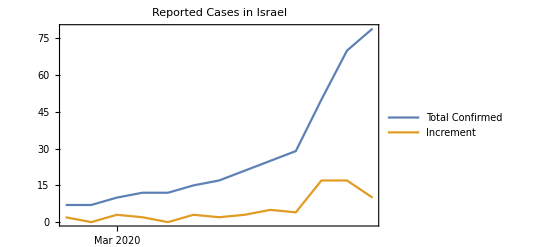

```mathematica
{PatientListNumber,PatientListIncrement}//DateListPlot[#,PlotLabel->"Reported Cases in Israel",PlotLegends->{"Total Confirmed","Increment"}]&
```